```mathematica
(*displayData=Import["displayTbl.fits","Table"];*)
rawdata=Import["C:\\Users\\DELL\\Downloads\\GRB_Redshit_List_final_lat.txt", "Table"];
(** Only GRBs with TS > 20.0 and fitted with SPL are selected. **)
```

```mathematica
rawdata[[1]]
```

{GRB_NAME,GBM_ID,OPT,OPT_beta,XRT,GBM,LAT,z,AG_temp_decay_model,BPL_temp_ind1,BPL_temp_ind1_err,BPL_temp_ind2,BPL_temp_ind2_err,SPL_temp_ind1,SPL_temp_ind1_err,LAT_spec_ind,LAT_spec_err_ind}

```mathematica
sigdata=SortBy[Select[rawdata,(#[[10]]*#[[11]]!=0.0)&],#[[12]]&];
```

```mathematica
sigdata
```

{{100414A,100414097,Y,Y,Y,Y,Y,1.37,BPL,1.804,0.217,0.315,0.55,1.266,0.13,-1.801,0.118},{080916C,80916009,Y,Y,Y,Y,Y,4.35,BPL,1.609,0.213,0.359,0.288,1.128,0.118,-1.86,0.536},{110731A,110731465,Y,Y,Y,Y,Y,2.83,BPL,1.771,0.114,0.389,1.071,1.534,0.117,-2.288,0.155},{221009A,221009553,Y,Y,Y,Y,Y,0.151,BPL,1.58,0.46,0.85,0.23,1.15,0.13,-1.79,0.05},{171010A,171010792,Y,Y,Y,Y,Y,0.33,BPL,2.24,0.733,0.969,0.294,1.318,0.158,-2.043,0.129},{090328A,90328401,Y,Y,Y,Y,Y,0.74,BPL,0.73,0.43,1.058,0.141,0.995,0.087,-2.204,0.131},{090926A,90926181,Y,Y,Y,Y,Y,2.11,BPL,1.765,0.168,1.103,0.171,1.393,0.078,-2.138,0.054},{090323A,90323002,Y,Y,Y,Y,Y,3.57,BPL,0.584,2.448,1.122,0.17,1.094,0.134,-2.29,0.154},{090902B,90902462,Y,Y,Y,Y,Y,1.82,BPL,1.866,0.17,1.237,0.231,1.634,0.079,-1.941,0.042},{160509A,160509374,Y,Y,Y,Y,Y,1.17,BPL,0.879,0.266,1.338,0.303,1.125,0.115,-2.382,0.119},{090510A,90510016,Y,Y,Y,Y,Y,0.9,BPL,2.316,0.175,1.341,0.18,1.813,0.083,-2.052,0.063},{130427A,130427324,Y,Y,Y,Y,Y,0.34,BP,0.789,0.161,1.423,0.104,1.24,0.062,-1.986,0.039},{180720B,180720598,Y,Y,Y,Y,Y,0.654,BPL,1.458,0.187,3.198,0.564,1.883,0.145,-2.23,0.097}}

```mathematica
fullabplot={};
Do[
alpha=sigdata[[i,12]];
beta=-1*sigdata[[i,16]] -1;
aErr = sigdata[[i,13]];
bErr = sigdata[[i,17]];
If[alpha*beta!=0.0,
AppendTo[fullabplot,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}]];
,{i,1,Length[sigdata]}];
```

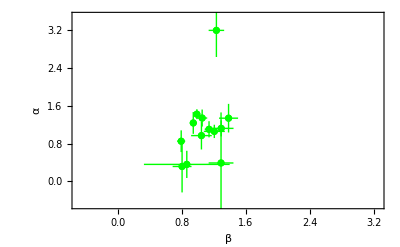

```mathematica
fullrelation=ListPlot[fullabplot,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
Show[fullrelation,PlotRange->{{-0.5,3.25},{-0.5,3.5}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","All GRBs"}}]
```

```mathematica
k=0; 

(* Indices *)
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowLesserSPL = {};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};
totalsampleBPL = {};
totalsampleSPL = {};
headerline = {"beta", "betaErr", "alpha", "alphaErr"};
AppendTo[totalsampleBPL, headerline];
AppendTo[totalsampleSPL, headerline];

(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
alpha1=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr1= sigdata[[i,11]];
aErr=sigdata[[i,13]];
bErr = sigdata[[i,17]];
idGRB = sigdata[[i, 1]]; 

If[alpha1*beta*aErr1*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha1-aErr1},{beta+bErr,alpha1+aErr1}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha1)^2/(aErr1)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha1-aErr1-0.1,alpha1+aErr1+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[totalsampleBPL, {beta, bErr, alpha1, aErr1}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=0*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[4x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesser,i];
AppendTo[plotSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}]; (*relation is a = b-1*)
(*r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];*)
(*regUni=RegionUnion[r1,r2];*)
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsGreaterBPL, idGRB]; 
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=0!!!!!!!*)
r1=ImplicitRegion[(x-1)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
 
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
]


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[totalsampleSPL, {beta, bErr, alpha, aErr}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=0*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[4x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesserSPL,i];
AppendTo[plotSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowLesserSPL, idGRB]; 
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=0!!!!!!!*)
r1=ImplicitRegion[(x-1)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB]; 
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
]


]
],{i,1,Length[sigdata]}];
```

```mathematica
Export["totalsampleBPLinj.txt", totalsampleBPL, "Table"];
Export["totalsampleSPLinj.txt", totalsampleSPL, "Table"];
```

```mathematica
actualtotalk0= DeleteDuplicates[totalsample]
```

{080916C,110731A,090323A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{080916C,110731A,090323A}

{}

{080916C,110731A,090323A}

{}

{}

Total Number of GRBs considered: 13

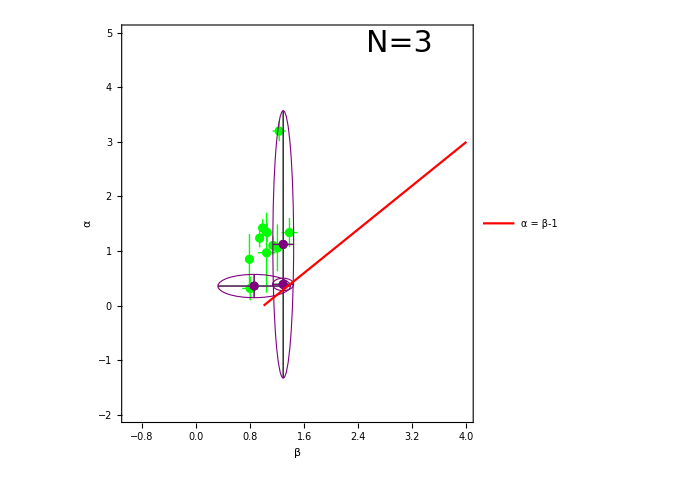

```mathematica
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotGreaterTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

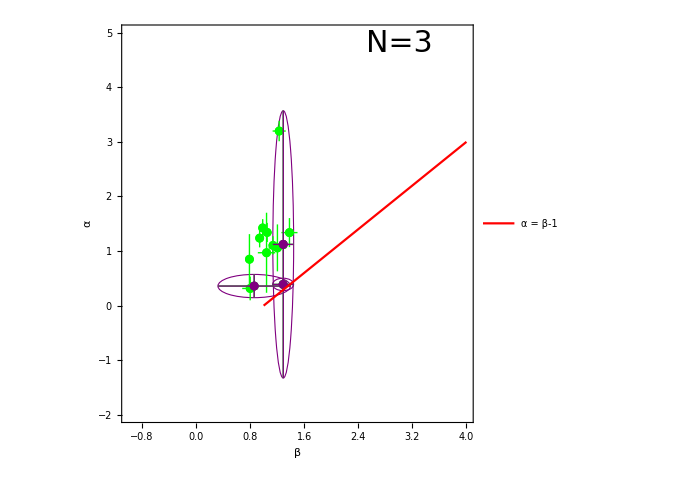

```mathematica
(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=0!!!!!!!*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

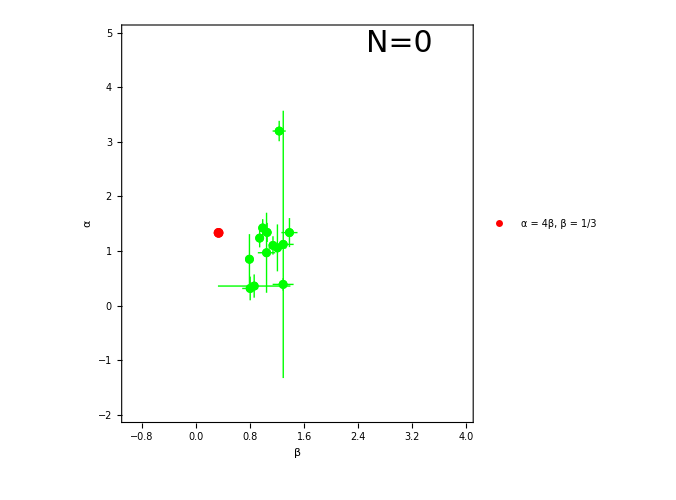

```mathematica
(*Slow Cooling, v < Subscript[v, m]*)
satbplplot=ListPlot[plotSlowLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowLesser]+Length[SlowLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{1/3,4/3}},PlotMarkers->{Automatic, Medium},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = 4β, β = 1/3"},{0.65,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotSlowLesserTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowLesser.pdf",Show[txt,plotSlowLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

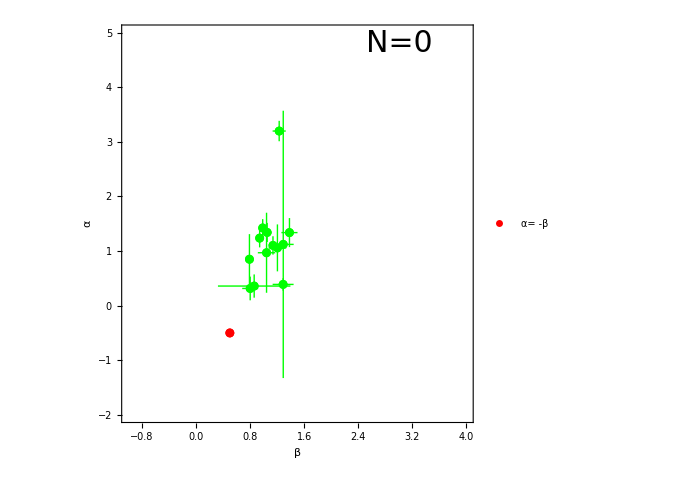

```mathematica
(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{0.5,-0.5}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastBetweenTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c < v < v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

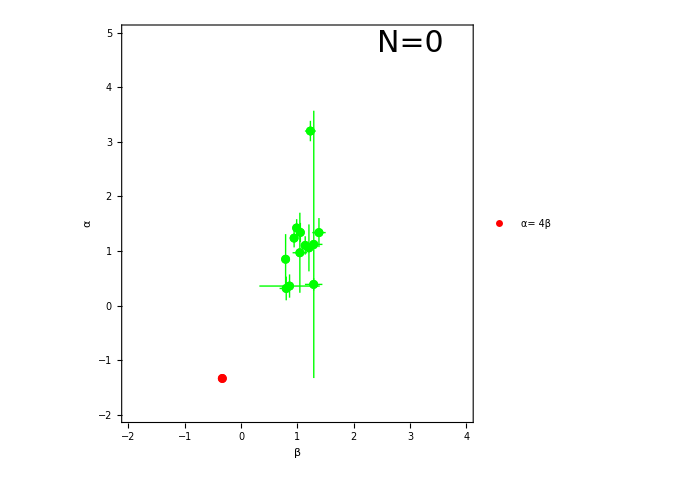

```mathematica
(* Fast Cooling, Subscript[v, c] > v *)
satbplplot=ListPlot[plotFastLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastLesser]+Length[FastLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{-(1/3),-(4/3)}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= 4β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastLesserTotErr,reg1,PlotRange->{{-2.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c > v"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastLesser.pdf",Show[txt,plotFastLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
K = 1 CASE
```

CASE

```mathematica
k=1; 

(* Indices *)
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowLesserSPL = {};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};

(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
alpha1=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr1= sigdata[[i,13]];
aErr=sigdata[[i,11]];
bErr = sigdata[[i,17]];
idGRB = sigdata[[i, 1]]; 


If[alpha1*beta*aErr1*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha1-aErr1},{beta+bErr,alpha1+aErr1}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha1)^2/(aErr1)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha1-aErr1-0.1,alpha1+aErr1+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];


(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=1*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[3x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesser,i];
AppendTo[plotSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}]; (*relation is a = b-1*)
(*r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];*)
(*regUni=RegionUnion[r1,r2];*)
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1!!!!!!!*)
r1=ImplicitRegion[(x-2/3)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
]


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=1*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[3x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesserSPL,i];
AppendTo[plotSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1!!!!!!!*)
r1=ImplicitRegion[(x-2/3)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
]


]
],{i,1,Length[sigdata]}];
```

```mathematica
actualtotalk1 = DeleteDuplicates[totalsample]
```

{100414A,080916C,110731A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{080916C,110731A}

{}

{100414A,080916C,110731A}

{}

{}

Total Number of GRBs considered: 13

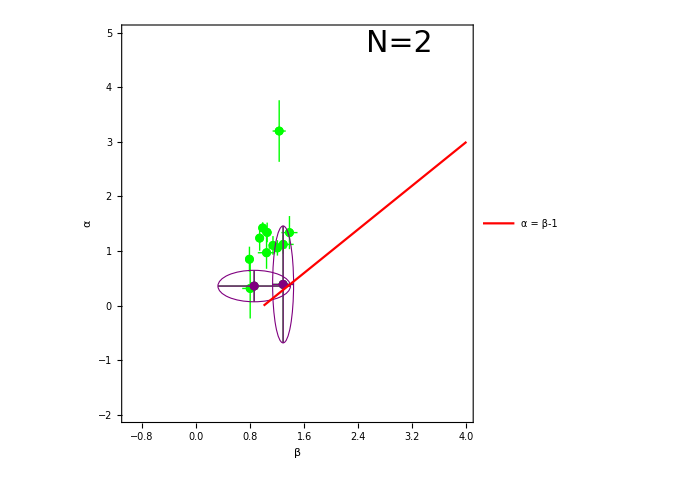

```mathematica
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotGreaterTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

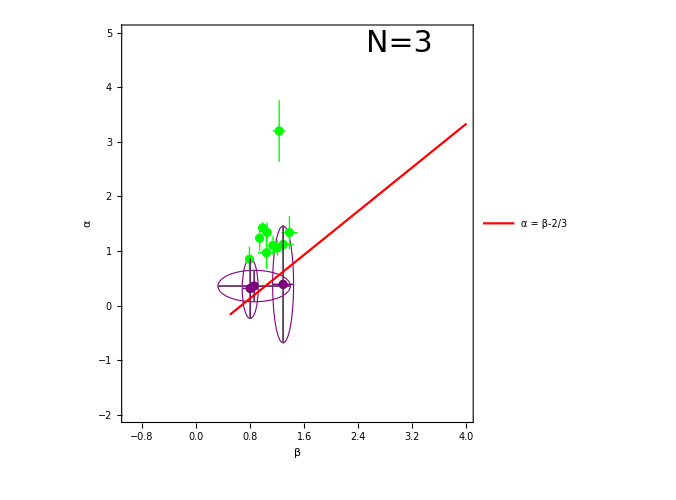

```mathematica
(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1!!!!!!!*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-2/3)},{x,0.5,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-2/3"},{0.65,0.8}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Slow Cooling, v_m < v < v_c"}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

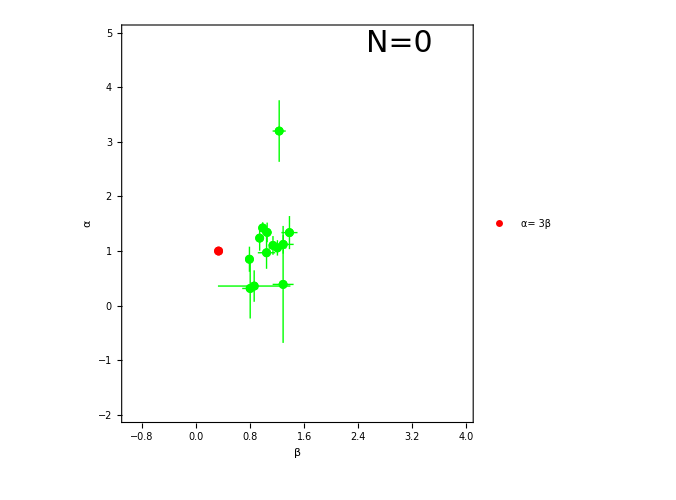

```mathematica
(*Slow Cooling, v < Subscript[v, m]*)
satbplplot=ListPlot[plotSlowLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowLesser]+Length[SlowLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{1/3,1}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= 3β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotSlowLesserTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowLesser.pdf",Show[txt,plotSlowLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

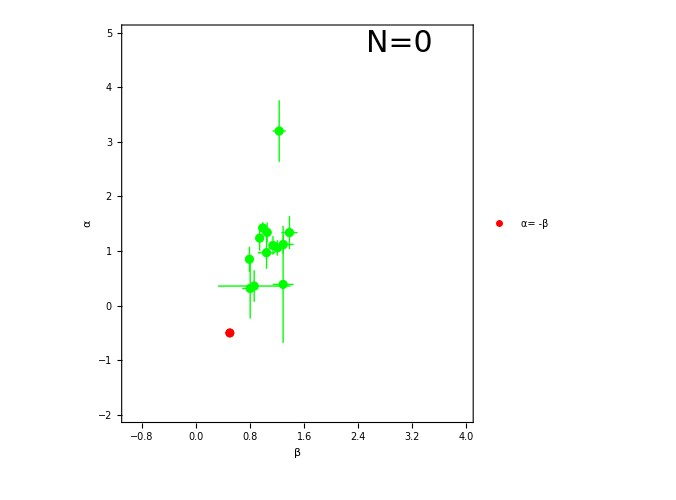

```mathematica
(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{0.5,-0.5}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastBetweenTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c < v < v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

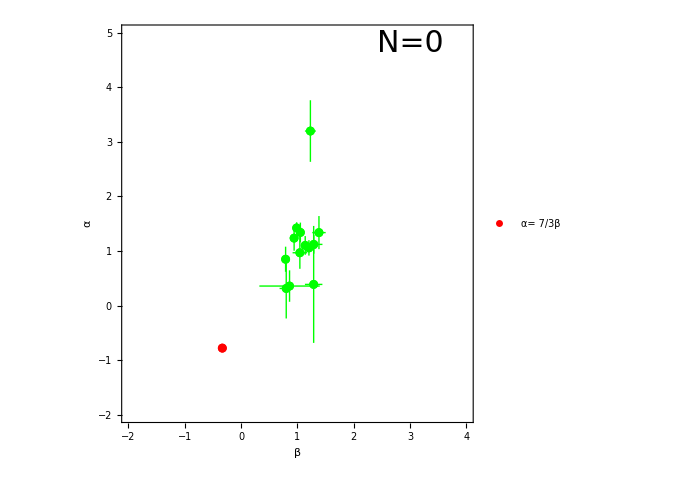

```mathematica
(* Fast Cooling, Subscript[v, c] > v *)
satbplplot=ListPlot[plotFastLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastLesser]+Length[FastLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{-1/3,-7/9}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= 7/3β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastLesserTotErr,reg1,PlotRange->{{-2.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c > v"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastLesser.pdf",Show[txt,plotFastLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

K = 1.5 CASE

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
k=1.5; 

(* Indices *)
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowLesserSPL = {};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};

(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
alpha1=sigdata[[i,10]];
alpha=sigdata[[i,12]];
beta=-1*sigdata[[i,16]] -1;
aErr1= sigdata[[i,11]];
aErr=sigdata[[i,13]];
bErr = sigdata[[i,17]];
idGRB = sigdata[[i, 1]]; 


If[alpha1*beta*aErr1*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha1-aErr1},{beta+bErr,alpha1+aErr1}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha1)^2/(aErr1)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha1-aErr1-0.1,alpha1+aErr1+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];


(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=1.5*)
(*r1=ImplicitRegion[(x*(7k-16)/(4-k))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[11/5 x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesser,i];
AppendTo[plotSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}]; (*relation is a = b-1*)
(*r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];*)
(*regUni=RegionUnion[r1,r2];*)
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1.5!!!!!!!*)
r1=ImplicitRegion[(x-(2/5))==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
]


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=1.5*)
(*r1=ImplicitRegion[(x*(7k-16)/(4-k))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[11/5 x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesserSPL,i];
AppendTo[plotSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1.5!!!!!!!*)
r1=ImplicitRegion[(x-(2/5))==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
]


]
],{i,1,Length[sigdata]}];
```

```mathematica
actualtotalk15 = DeleteDuplicates[totalsample]
```

{090328A,090323A,160509A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{090323A}

{}

{090328A,090323A,160509A}

{}

{}

Total Number of GRBs considered: 13

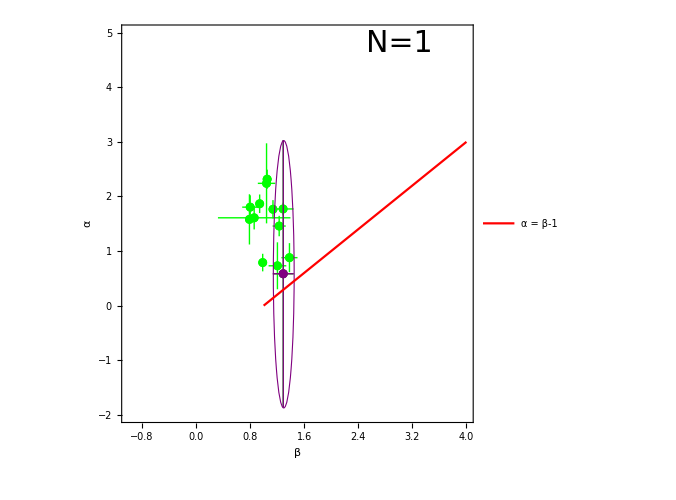

```mathematica
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotGreaterTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

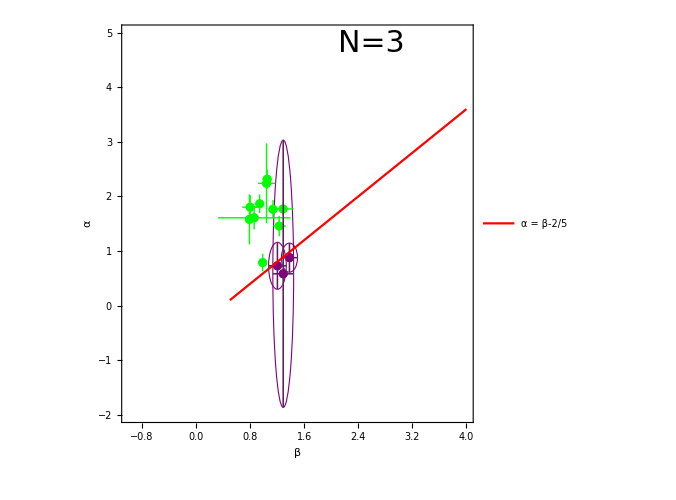

```mathematica
(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=1.5!!!!!!!*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{2.6,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-(2/5))},{x,0.5,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-2/5"},{0.65,0.85}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Slow Cooling, v_m < v < v_c"}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

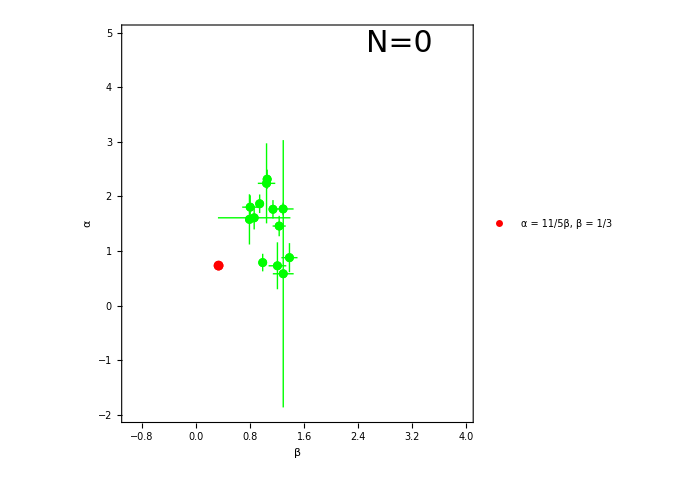

```mathematica
(*Slow Cooling, v < Subscript[v, m]*)
satbplplot=ListPlot[plotSlowLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowLesser]+Length[SlowLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{1/3,11/15}},PlotMarkers->{Automatic, Medium},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = 11/5β, β = 1/3"},{0.65,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotSlowLesserTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowLesser.pdf",Show[txt,plotSlowLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

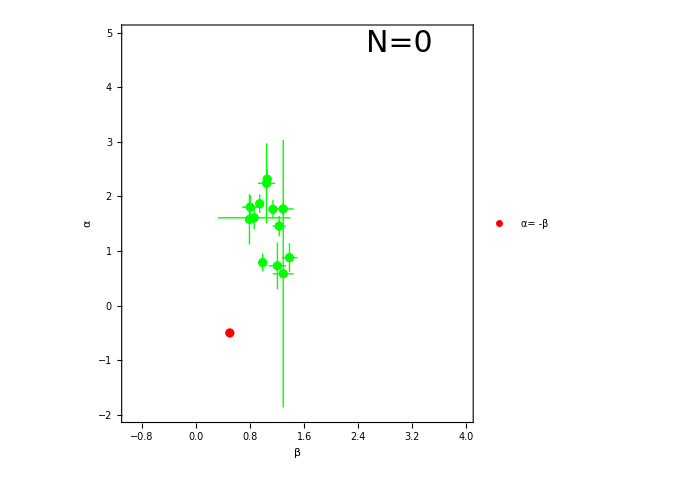

```mathematica
(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{0.5,-0.5}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastBetweenTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c < v < v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

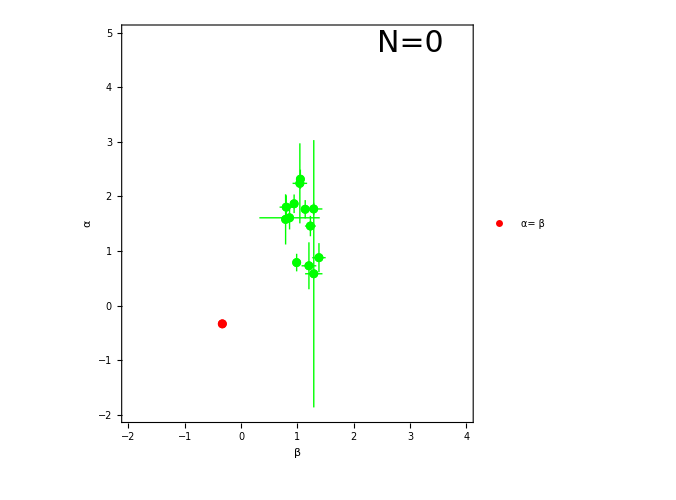

```mathematica
(* Fast Cooling, Subscript[v, c] > v *)
satbplplot=ListPlot[plotFastLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastLesser]+Length[FastLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{-1/3,-1/3}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastLesserTotErr,reg1,PlotRange->{{-2.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c > v"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastLesser.pdf",Show[txt,plotFastLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
k=2; 

(* Indices *)
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowLesserSPL = {};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};


(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
alpha1=sigdata[[i,10]];
alpha=sigdata[[i,12]];
beta=-1*sigdata[[i,16]] -1;
aErr1= sigdata[[i,11]];
aErr=sigdata[[i,13]];
bErr = sigdata[[i,17]];
idGRB = sigdata[[i, 1]]; 




If[alpha1*beta*aErr1*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha1-aErr1},{beta+bErr,alpha1+aErr1}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha1)^2/(aErr1)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha1-aErr1-0.1,alpha1+aErr1+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];


(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=2*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesser,i];
AppendTo[plotSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}]; (*relation is a = b-1*)
(*r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];*)
(*regUni=RegionUnion[r1,r2];*)
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2!!!!!!!*)
r1=ImplicitRegion[(x)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
]


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=2*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesserSPL,i];
AppendTo[plotSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2!!!!!!!*)
r1=ImplicitRegion[(x)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
]


]
],{i,1,Length[sigdata]}];
```

```mathematica
actualtotalk2 = DeleteDuplicates[totalsample]
```

{090323A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{090323A}

{}

{090323A}

{}

{}

```mathematica
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotGreaterTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

Total Number of GRBs considered: 13

-Graphics-

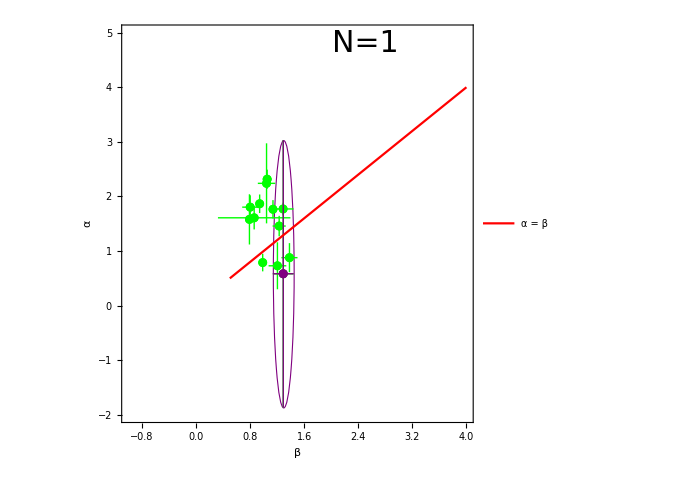

```mathematica
(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2!!!!!!!*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{2.5,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x)},{x,0.5,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β"},{0.65,0.83}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Slow Cooling, v_m < v < v_c"}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

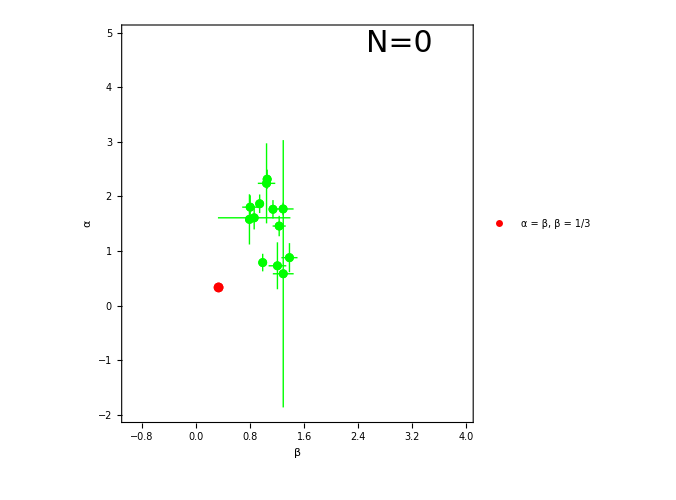

```mathematica
(*Slow Cooling, v < Subscript[v, m]*)
satbplplot=ListPlot[plotSlowLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowLesser]+Length[SlowLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{1/3,1/3}}, PlotMarkers->{Automatic, Medium},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β, β = 1/3"},{0.65,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotSlowLesserTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowLesser.pdf",Show[txt,plotSlowLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{0.5,-0.5}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastBetweenTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c < v < v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

-Graphics-

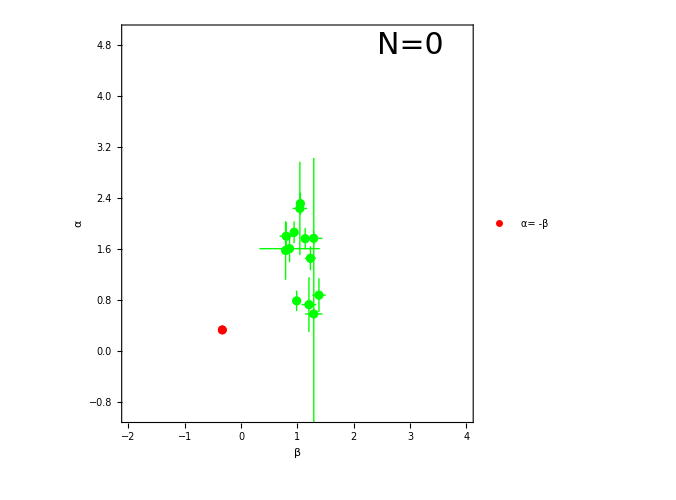

```mathematica
(* Fast Cooling, Subscript[v, c] > v *)
satbplplot=ListPlot[plotFastLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastLesser]+Length[FastLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{-(1/3),1/3}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastLesserTotErr,reg1,PlotRange->{{-2.0,4.0},{-1.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c > v"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastLesser.pdf",Show[txt,plotFastLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
K = 2.5
```

2.5

```mathematica
k=2.5; 

(* Indices *)
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowLesserSPL = {};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};

(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
alpha1=sigdata[[i,10]];
alpha=sigdata[[i,12]];
beta=-1*sigdata[[i,16]] -1;
aErr1= sigdata[[i,11]];
aErr=sigdata[[i,13]];
bErr = sigdata[[i,17]];
idGRB = sigdata[[i, 1]]; 


If[alpha1*beta*aErr1*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha1-aErr1},{beta+bErr,alpha1+aErr1}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha1)^2/(aErr1)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha1-aErr1-0.1,alpha1+aErr1+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];


(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=2.5*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[-x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesser,i];
AppendTo[plotSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}]; (*relation is a = b-1*)
(*r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];*)
(*regUni=RegionUnion[r1,r2];*)
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2.5!!!!!!!*)
r1=ImplicitRegion[(x+2/3)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha1,aErr1]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
]


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha1},{bErr,aErr1}]}]}];

(*Slow Cooling, v < Subscript[v, m]*)(*WATCH!!!!! YOU MADE THIS SPECIFIC TO K=2.5*)
(*r1=ImplicitRegion[(x*((7k-16)/(4-k)))==y,{{x,0.33,0.33},y}];*)
r1=ImplicitRegion[-x==y,{{x,0.33,0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowLesserSPL,i];
AppendTo[plotSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(x-1)==y,{{x,1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2.5!!!!!!!*)
r1=ImplicitRegion[(x+2/3)==y,{{x,0.5,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[-x==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] > v *)
r1=ImplicitRegion[(x*((16-9k)/(4-k)))==y,{{x,-0.33,-0.33},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
]


]
],{i,1,Length[sigdata]}];
```

```mathematica
actualtotalk25 = DeleteDuplicates[totalsample]
```

{080916C,110731A,221009A,171010A,090926A,090323A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{090323A}

{}

{080916C,110731A,221009A,171010A,090926A,090323A}

{}

{}

```mathematica
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(* v > Subscript[v, c],Subscript[v, m]*) (*both slow and fast cooling*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x-1)},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = β-1"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotGreaterTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

Total Number of GRBs considered: 13

-Graphics-

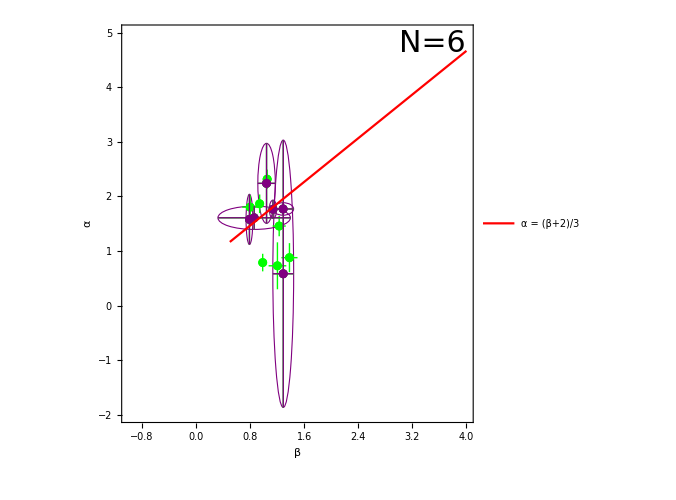

```mathematica
(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)(*SPECIFIC TO k=2.5!!!!!!!*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.5,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(x+2/3)},{x,0.5,4.0},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (β+2)/3"},{0.7,0.8}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Slow Cooling, v_m < v < v_c"}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

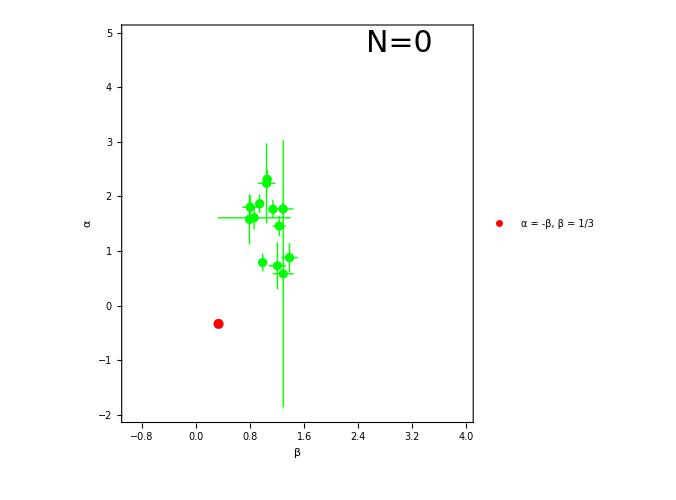

```mathematica
(*Slow Cooling, v < Subscript[v, m]*)
satbplplot=ListPlot[plotSlowLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowLesser]+Length[SlowLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{1/3,(-1)/3}},PlotMarkers->{Automatic, Medium}, PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = -β, β = 1/3"},{0.65,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotSlowLesserTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"SlowLesser.pdf",Show[txt,plotSlowLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{0.5,-0.5}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= -β"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastBetweenTotErr,reg1,PlotRange->{{-1.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c < v < v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

-Graphics-

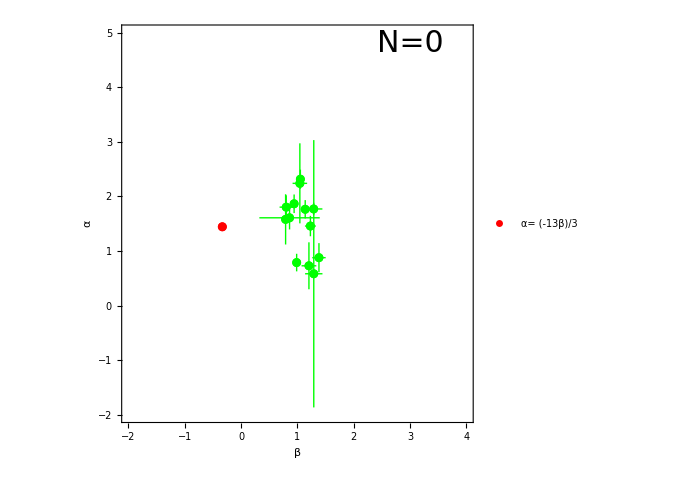

```mathematica
(* Fast Cooling, Subscript[v, c] > v *)
satbplplot=ListPlot[plotFastLesserBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastLesserSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastLesser]+Length[FastLesserSPL]],FontSize->30],{3.0,4.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},ListPlot[{{-(1/3),13/9}},PlotRange->{{-1.0,4.0},{-2.0,5.0}},PlotStyle->{Red},PlotLegends->Placed[{"α= (-13β)/3"},{0.7,0.8}]]];
Show[txt,totalplot,satbplplot,satsplplot,plotFastLesserTotErr,reg1,PlotRange->{{-2.0,4.0},{-2.0,5.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", Fast Cooling, v_c > v"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["wplotk"<>ToString[k]<>"FastLesser.pdf",Show[txt,plotFastLesserTotErr,totalplot,satbplplot,satsplplot,reg1, PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
```

```mathematica
totalwithinj = DeleteDuplicates[Join[actualtotalk0, actualtotalk1, actualtotalk15, actualtotalk2, actualtotalk25]]
```

{090323A,090328A,160509A,080916C,110731A,221009A,171010A,090926A}

```mathematica
Length[totalwithinj]
```

8

```mathematica
18 - 8
```

10